# Compute EWS from a toy model

## Setup

```mathematica
(* Set a directory *)
SetDirectory["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/toy_models"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
```

## Toy Model 1

Model dX = kX(1-X)(-X+w)dt + σdW(t)

### Key parameters

```mathematica
dt=0.1; (* time step *)
tmax=100; (* max time (simulation stop *)
σ=0.01; (* noise intensity *)
k=7; (* model parameteres *)
ωh=1.2; (* max control param *)
ωl=0; (* min control param *)
x0=1; (* initial condition *)
seed=2; (* seed number *)
numSims=2; (* number of simulations *)

(* lag autocorrelation *)
tau=0.25; (* in units of time *)
pointLag=Floor[(tau/tmax)*numComps];

detrendOp=1; (* 1 for yes, 0 for no *)
bandWidth=0.5; (* for Gaussian filtering (as a percentage) *)
rollWindow=0.2; (* for indicator calculation *)
```

### Model details

```mathematica
(* Clear function labels *)
Clear[f,x]
```

```mathematica
(* Dynamic equations *)
fun[x_,w_]:=k x(1-x) (x-w);
```

```mathematica
(* Find equilibria *)
equilibria=Solve[fun[x,w]==0 ,x]
```

{{x→0},{x→1},{x→w}}

```mathematica
(* Initial equilibiria *)
xeq=x/.equilibria[[2]];
```

### Stochastic Simulation

Simulate the SDE dX = kX(1-X)(-X+w)dt + σdW(t)

```mathematica
(* clear function labels *)
Clear[stochProc]
```

```mathematica
(* risk evolution *)
Clear[ω]
ω[t_]:=((ωh-ωl)/tmax) t +ωl;

(* Critical time *)
tcrit=tmax*((1-ωl)/(ωh-ωl));
```

```mathematica
(* define the stocahstic process *)
stochProc[k_,ω_,x0_,σ_]:=ItoProcess[ⅆx[t]==k x[t](1-x[t])(x[t]-ω[t])ⅆt+σ ⅆw[t],x[t],{x,x0},t,w\[Distributed]WienerProcess[]]
```

```mathematica
(* Simulation *)
SeedRandom[seed];
stochSol[k_,ω_,x0_,σ_]:=RandomFunction[stochProc[k,ω,x0,σ],{0,tmax,dt},numSims,Method->"EulerMaruyama"]
```

```mathematica
stochData=stochSol[k,ω,x0,σ]
```

TemporalData[…]

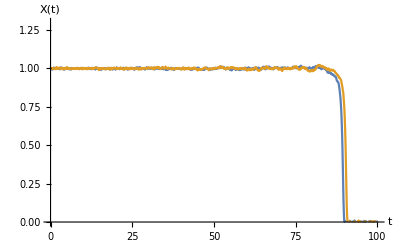

```mathematica
ListPlot[stochSol[k,ω,x0,σ],
Joined->True,
PlotRange->{0,1.3},
LabelStyle->14,
AxesLabel->{"t","X(t)"}]
```

### Simulation Indicators

#### Fit Gaussian (detrend)

```mathematica
pathData=stochData["Paths"];
pathData//Dimensions
(* num sims, time steps, (t,x) *)
```

{2,1001,2}

```mathematica
tVals=pathData[[1,;;,1]];
xVals=pathData[[;;,;;,2]]; (* form [x1;x2;,...;xn] *)
xVals//Dimensions
```

{2,1001}

```mathematica
(* work with data only up to tcrit *)
idxCrit=FirstPosition[tVals,x_/;x>=tcrit][[1]]-1;
tValsShort=tVals[[1;;idxCrit]];
```

```mathematica
(* find the fitting function for each realisation (if specified) *)
dataFit=If[detrendOp==1,
Table[GaussianFilter[xVals[[i,1;;idxCrit]],Length[tValsShort]*bandWidth],{i,1,numSims}],
ConstantArray[0,{numSims,idxCrit}]];
dataFit//Dimensions
```

{2,834}

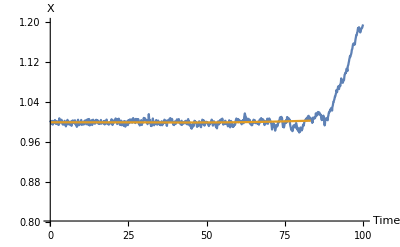

```mathematica
(* plot of a single realisation fitted *)
fitPlot=ListPlot[{{tVals,xVals[[1]]}ᵀ,{tValsShort,dataFit[[1]]}ᵀ},
Joined->True,
PlotRange->{All,{0.8,1.2}},
ImageSize->400,
LabelStyle->14,
AxesLabel->{"Time","X"}]
```

#### Residuals

{2,834}

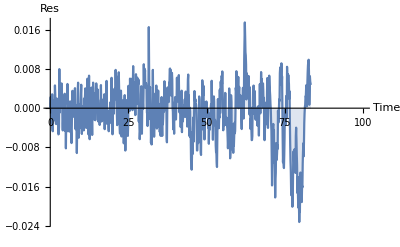

```mathematica
residuals=xVals[[;;,1;;idxCrit]]-dataFit;
residuals//Dimensions
residPlot=ListPlot[{tValsShort,residuals[[1]]}ᵀ,
Joined->True,
Filling->Axis,
AxesLabel->{"Time","Res"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All}]
```

#### Standard Deviation of Residuals

```mathematica
windowComps=Round[rollWindow*Length[tVals]];
sdSeries=Table[MovingMap[StandardDeviation,residuals[[i]],windowComps],{i,1,numSims}]; (* has form [s1;s2;...;sn] *)
sdSeries//Dimensions
```

{2,634}

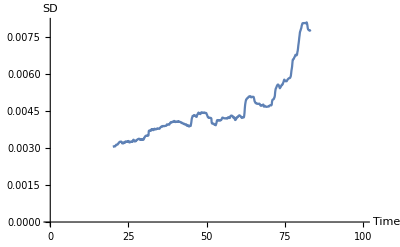

```mathematica
(* a single plot *)
sdPlot=ListPlot[{tValsShort[[windowComps+1;;]],sdSeries[[1]]}ᵀ, (* to account for the rolling window *)
Joined->True,
AxesLabel->{"Time","SD"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},Automatic}]
```

```mathematica
(* a plot averaged over simulations *)
meanSDseries=Mean[sdSeries];
devSDseries=StandardDeviation[sdSeries];
```

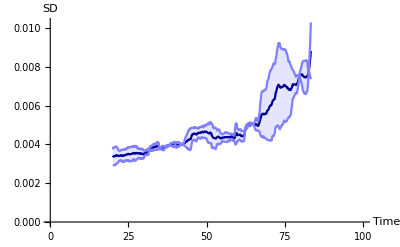

```mathematica
sdAvPlot=ListPlot[{{tValsShort[[windowComps+1;;]],meanSDseries}ᵀ,
{tValsShort[[windowComps+1;;]],meanSDseries+devSDseries}ᵀ,
{tValsShort[[windowComps+1;;]],meanSDseries-devSDseries}ᵀ},
Joined->True,
PlotStyle->{Darker[Blue,0.4],Lighter[Blue,0.5],Lighter[Blue,0.5]},
Filling->{{2->{1}},{3->{1}}},
AxesLabel->{"Time","SD"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},Automatic}]
```

#### Autocorrelation of Residuals

```mathematica
(* form [a1;a2;,,,;an] *)
acSeries=Table[MovingMap[CorrelationFunction[#,pointLag]&,residuals[[i]],windowComps],{i,1,numSims}]; 
acSeries//Dimensions
```

{2,634}

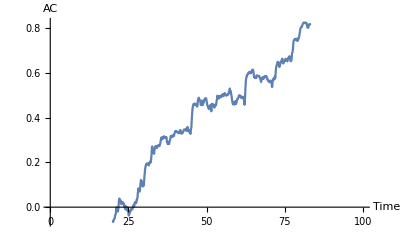

```mathematica
(* Plot for single realisation *)
acPlot=ListPlot[{tValsShort[[windowComps+1;;]],acSeries[[1]]}ᵀ,
Joined->True,
AxesLabel->{"Time","AC"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All}]
```

```mathematica
(* a plot averaged over simulations *)
meanACseries=Mean[acSeries];
devACseries=StandardDeviation[acSeries];
```

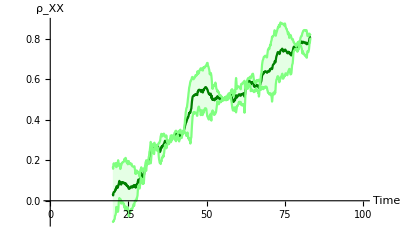

```mathematica
acAvPlot=ListPlot[{{tValsShort[[windowComps+1;;]],meanACseries}ᵀ,
{tValsShort[[windowComps+1;;]],meanACseries+devACseries}ᵀ,
{tValsShort[[windowComps+1;;]],meanACseries-devACseries}ᵀ},
Joined->True,
PlotStyle->{Darker[Green,0.5],Lighter[Green,0.5],Lighter[Green,0.5]},
Filling->{{2->{1}},{3->{1}}},
AxesLabel->{"Time","ρ_XX"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},Automatic}]
```

### Plots

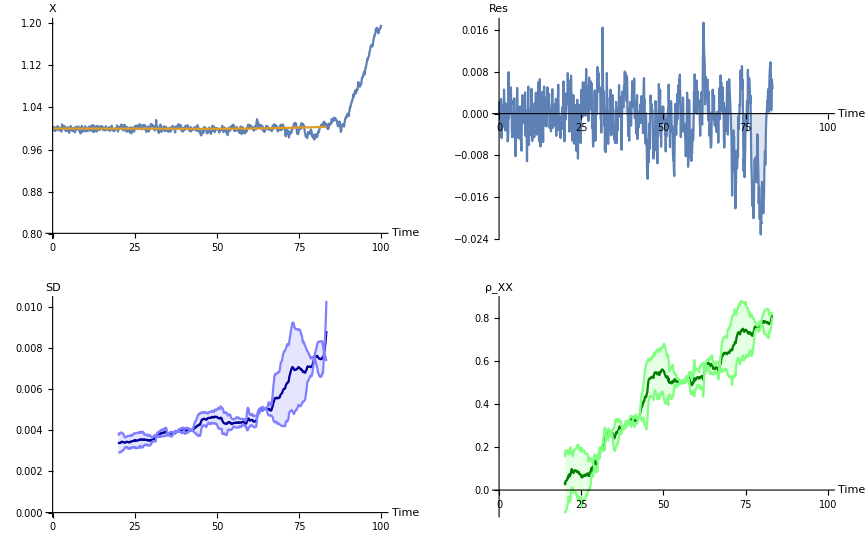

```mathematica
toy1Plots=GraphicsGrid[{{fitPlot,residPlot},{sdAvPlot,acAvPlot}}]
```

```mathematica
(* Export["figures/toy1plots.pdf",toy1Plots]; *)
```

### OU Indicators

Since 1D system - OU variance and AC are computed analytically by hand - in excellent agreement with simulations.

```mathematica
Clear[ω]
lambda=k(ω-1);
var=-σ^2/(2 lambda);
sd= Sqrt[var];
ac=Exp[lambda tau];
```

```mathematica
acOUPlot=Plot[ac,{ω,0,1},
LabelStyle->TMBFS12,
AxesLabel->{"ω","AC"},
PlotRange->{0,1}];
```

```mathematica
sdOUPlot=Plot[sd,{ω,0,1},
LabelStyle->TMBFS12,
AxesLabel->{"ω","SD"},
PlotRange->{0,0.03}];
```

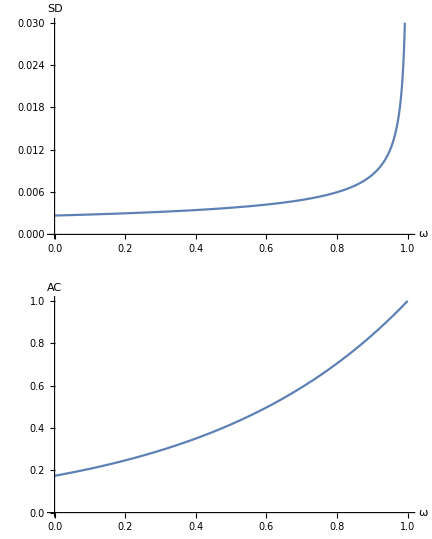

```mathematica
ouPlots=GraphicsColumn[{sdOUPlot,acOUPlot}]
```

```mathematica
Export["figures/ouPlots.pdf",ouPlots];
```